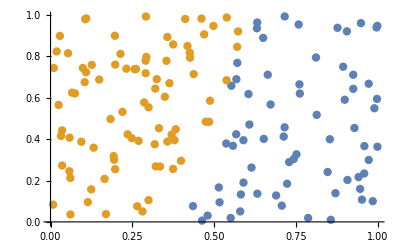

```mathematica
d=2;
n=150;
x=Table[Table[RandomReal[],{j,1,d}],{i,1,n}];
k=2;

Cost[m_,P_,k_,d_]:=Sum[Sum[Sum[(x[[i,l]]-m[[j,l]])^2,{l,1,d}],{i,P[[j]]}],{j,1,k}]
kMeans[x_,k_]:=Module[{n=Length[x],d=Length[x[[1]]],m=List[],S=List[],j,prev=Infinity,i,C},
m=Table[x[[j]],{j,1,k}];
For[i=1,i<=k-1,i++,AppendTo[S,{i}]];
AppendTo[S,Range[k,n]];
C=Cost[m,S,k,d];
While[C<prev,
prev=C;
For[j=1,j<=k,j++,S[[j]]={}];
For[i=1,i<=n,i++,
AppendTo[S[[Flatten[Position[m,Flatten[Nearest[m,x[[i]]]]]][[1]]]],i]
];
For[j=1,j<=k,j++,
m[[j]]=Sum[x[[i]],{i,S[[j]]}]/Length[S[[j]]]
];
C=Cost[m,S,k,d];
];
Return[Table[Table[x[[i]],{i,S[[j]]}],{j,1,k}]]
]

If[d==3,ListPointPlot3D[kMeans[x,k],PlotStyle->{PointSize[0.02]}],If[d==2,ListPlot[kMeans[x,k],PlotStyle->{PointSize[0.015]}],If[d==1,NumberLinePlot[kMeans[x,k],PlotStyle->{PointSize[0.003]}]]]]
MatrixForm[x];
```

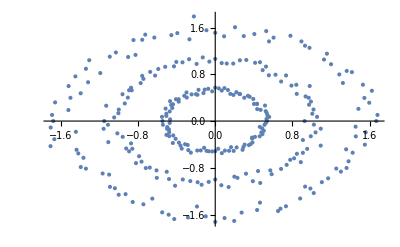

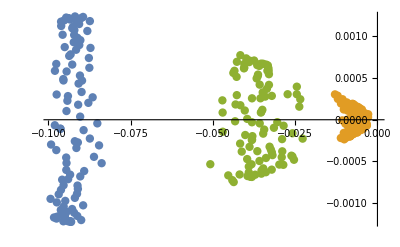

{{{-0.0876938,0.000741791},{-0.0927534,0.000662762},{-0.0932359,0.000785469},{-0.0875501,0.00062408},{-0.0872072,0.000862805},{-0.0904067,0.000531075},{-0.0906081,0.000897427},{-0.0897727,0.000470091},{-0.0902828,0.000955499},{-0.0908256,0.000434386},{-0.0921689,0.00101838},{-0.0899122,0.000333482},{-0.08816,0.00106625},{-0.0865454,0.000269301},{-0.0927467,0.00109874},{-0.087852,0.000202996},{-0.0906611,0.00114925},{-0.0909497,0.000180362},{-0.0915078,0.00116417},{-0.090344,0.0000374265},{-0.0873888,0.00118482},{-0.085127,-0.0000436746},{-0.0934624,0.00120418},{-0.0893,-0.000124888},{-0.0900087,0.00122124},{-0.0873934,-0.000225848},{-0.0917715,0.00122624},{-0.0910441,-0.000272505},{-0.0919076,0.00124056},{-0.0846006,-0.000307814},{-0.0945851,0.00122737},{-0.091488,-0.000339156},{-0.0894601,0.00123482},{-0.0861438,-0.000445474},{-0.0938049,0.00122046},{-0.0838165,-0.000521945},{-0.0952053,0.00119312},{-0.0891229,-0.000616034},{-0.096142,0.00117824},{-0.0903123,-0.000680621},{-0.0911616,0.00117202},{-0.0939991,-0.000713817},{-0.0961086,0.00112605},{-0.0911449,-0.000790403},{-0.0925447,0.00111648},{-0.0910338,-0.00083101},{-0.0921098,0.00107631},{-0.0912977,-0.000888962},{-0.0956747,0.00102072},{-0.0919513,-0.000938488},{-0.0911892,0.000984175},{-0.0948736,-0.000974828},{-0.0922992,0.000930989},{-0.0894396,-0.00102804},{-0.0950326,0.000872566},{-0.0927877,-0.00107225},{-0.0915785,0.000840683},{-0.0921847,-0.00111686},{-0.0936753,0.000766438},{-0.0961329,-0.00113621},{-0.0976031,0.000670216},{-0.091213,-0.00115548},{-0.0980078,0.000587808},{-0.0948627,-0.00118513},{-0.0944619,0.000579829},{-0.0900287,-0.00120484},{-0.09547,0.00048834},{-0.093274,-0.00121823},{-0.0954151,0.000471714},{-0.0954492,-0.00121989},{-0.0974883,0.00030307},{-0.093097,-0.00122699},{-0.0940534,0.0002841},{-0.0933364,-0.00122539},{-0.0942249,0.000227911},{-0.0940489,-0.00121884},{-0.0945001,0.000104699},{-0.0975268,-0.00118701},{-0.098045,-0.0000660604},{-0.0982896,-0.00117411},{-0.0963288,-0.000107008},{-0.0973721,-0.00116444},{-0.0963723,-0.000109341},{-0.0949655,-0.00114853},{-0.0919628,-0.000258047},{-0.0944815,-0.00110741},{-0.0991774,-0.000297609},{-0.0962188,-0.00108329},{-0.0975974,-0.000364498},{-0.0953484,-0.00104296},{-0.0945883,-0.000454109},{-0.0974382,-0.000992627},{-0.0944889,-0.000519891},{-0.0993455,-0.000950156},{-0.0945573,-0.000603406},{-0.0968643,-0.000895431},{-0.0933932,-0.000659191},{-0.0961718,-0.000842269},{-0.0958166,-0.000720015},{-0.0953818,-0.000786499}},{{-0.00392383,0.0000644719},{-0.00347464,0.0000524219},{-0.00370706,0.0000665744},{-0.00902492,0.000108578},{-0.00693611,0.000124294},{-0.00367404,0.0000440358},{-0.00385325,0.0000792146},{-0.00285475,0.0000304222},{-0.0066595,0.000136482},{-0.00738322,0.0000558738},{-0.00904147,0.00018747},{-0.00731867,0.0000481006},{-0.00505323,0.000116155},{-0.00795451,0.0000407683},{-0.00929866,0.000208114},{-0.00565141,0.0000189863},{-0.00510615,0.000124077},{-0.0064316,0.0000165467},{-0.00582029,0.000144954},{-0.00925066,7.29904×10^-7},{-0.0106213,0.000246339},{-0.0106886,-7.74697×10^-6},{-0.0047185,0.000123079},{-0.00664658,-0.0000211211},{-0.00759243,0.000191674},{-0.0070757,-0.0000275103},{-0.0073815,0.000188076},{-0.00568986,-0.0000308337},{-0.0121063,0.000288721},{-0.0068324,-0.0000407597},{-0.012911,0.00030457},{-0.00521471,-0.0000419326},{-0.00591048,0.000153695},{-0.00555782,-0.00005296},{-0.00689374,0.000174501},{-0.0087859,-0.0000837912},{-0.00542485,0.00013988},{-0.0044592,-0.0000575517},{-0.00741669,0.000182119},{-0.00412308,-0.0000577434},{-0.00804252,0.00018701},{-0.00326276,-0.0000499712},{-0.00758715,0.000174059},{-0.00403004,-0.0000667408},{-0.0120309,0.00025021},{-0.00850813,-0.000135267},{-0.00282352,0.0000664644},{-0.00466243,-0.0000853132},{-0.00759522,0.000154648},{-0.0032127,-0.0000646784},{-0.00901565,0.000172001},{-0.00413855,-0.0000848892},{-0.0110889,0.000195315},{-0.00327994,-0.0000718984},{-0.00611146,0.000109379},{-0.00555278,-0.000118975},{-0.0100007,0.000156155},{-0.00579395,-0.000130656},{-0.00807526,0.00012024},{-0.00886157,-0.000192751},{-0.00586996,0.0000835011},{-0.00421495,-0.000103802},{-0.0102286,0.00012338},{-0.00471288,-0.000115451},{-0.00772754,0.000095156},{-0.00501318,-0.000123439},{-0.00508852,0.0000556977},{-0.00609603,-0.000150421},{-0.00545129,0.0000467125},{-0.0100949,-0.000235297},{-0.00628499,0.0000453553},{-0.00610357,-0.000152247},{-0.00625378,0.0000388666},{-0.00823031,-0.000197637},{-0.00520421,0.0000146791},{-0.00836521,-0.000200016},{-0.00743174,0.000013714},{-0.00832534,-0.000197787},{-0.00739688,3.30699×10^-7},{-0.00937349,-0.000212834},{-0.00583445,-0.0000168388},{-0.00738437,-0.000173876},{-0.00842835,-0.000024525},{-0.00696397,-0.000162261},{-0.00509539,-0.0000182609},{-0.00789862,-0.000175615},{-0.00973659,-0.0000483716},{-0.00836215,-0.000174458},{-0.00494584,-0.0000344522},{-0.0111251,-0.000219241},{-0.00397384,-0.0000354055},{-0.00619156,-0.00012414},{-0.00610157,-0.0000598235},{-0.00953797,-0.000168134},{-0.00538383,-0.0000604944},{-0.00680038,-0.000118803},{-0.00877877,-0.000102602},{-0.0102219,-0.000158002},{-0.00426825,-0.0000622029},{-0.0045713,-0.0000723337}},{{-0.0245134,0.000306461},{-0.038262,-0.000535015},{-0.036294,0.000542449},{-0.0507956,-0.000534205},{-0.0395787,0.0000101437},{-0.036269,0.000663894},{-0.0327789,-0.000323819},{-0.0358925,0.000646737},{-0.0347285,-0.00016704},{-0.03381,0.000662267},{-0.0321324,-0.000599428},{-0.0471254,0.000232708},{-0.023753,0.00015723},{-0.0404764,0.000625686},{-0.0453379,-0.000668368},{-0.0380999,-0.000239207},{-0.0441133,-0.000725455},{-0.0336001,0.000371427},{-0.0286101,-0.000541315},{-0.0381419,-0.000030343},{-0.0272941,0.000306409},{-0.0329765,0.000418756},{-0.0395929,-0.00047244},{-0.036507,-0.000377388},{-0.0234556,0.000246345},{-0.0367151,0.000495936},{-0.0319008,-0.000424955},{-0.0412405,-0.000382451},{-0.034123,0.000278031},{-0.036383,0.000523431},{-0.0358608,-0.000495447},{-0.0388744,-0.000325292},{-0.0381253,0.000257267},{-0.0245029,0.00039709},{-0.0390984,-0.000562516},{-0.0417348,-0.000286423},{-0.043125,0.000183587},{-0.0404707,0.000670099},{-0.0258383,-0.000441134},{-0.0380082,-0.000197142},{-0.0349767,0.000119355},{-0.0334452,0.000589002},{-0.0347019,-0.000584165},{-0.040177,-0.000183558},{-0.0403195,0.000110998},{-0.0365433,0.000656242},{-0.0352348,-0.000610687},{-0.0470187,-0.000144177},{-0.0354295,0.0000860848},{-0.0389662,0.000692433},{-0.0394723,-0.000676351},{-0.0285237,-0.0000718938},{-0.0357758,-0.0000440278},{-0.0398867,0.000736926},{-0.0371543,-0.00066018},{-0.0432605,-0.0000185368},{-0.0304397,-0.0000291034},{-0.0374818,0.000711372},{-0.0386007,-0.000685797},{-0.0470509,0.0000862774},{-0.0338838,-0.00045914},{-0.0405653,0.000617049},{-0.0290901,-0.000450181},{-0.0434571,0.000587928},{-0.028928,-0.000379299},{-0.0329815,0.000546948},{-0.0261501,-0.000431755},{-0.0437964,0.000562338},{-0.0320854,-0.000392427},{-0.0427123,0.000696028},{-0.0418929,-0.00065756},{-0.0428056,0.000515079},{-0.0323786,-0.000359872},{-0.0330691,0.000588462},{-0.0390963,-0.000631855},{-0.0357927,0.000421588},{-0.022738,-0.000226867},{-0.033137,0.000619999},{-0.0298316,-0.000538381},{-0.0348729,0.000328255},{-0.0289823,-0.000232525},{-0.0388112,0.000709668},{-0.0253663,-0.0004807},{-0.0321048,0.000286492},{-0.0381728,-0.000243336},{-0.0353644,0.000673807},{-0.0436862,-0.000748442},{-0.0427419,0.000295425},{-0.0258299,-0.000162658},{-0.0347547,0.000672549},{-0.0381672,-0.000686951},{-0.0355574,0.000257474},{-0.0344155,-0.000117901},{-0.0416657,0.000775251},{-0.0339153,-0.000630383},{-0.0416607,0.0001742},{-0.0314647,-0.0000965755},{-0.0333125,0.000652219},{-0.0352774,-0.000647627},{-0.0352959,0.0000939706}}}

```mathematica
n=100;
k=3;
m=2;
R[]:=RandomReal[{0.95,1.1}]
x=Map[R[]*#&,Union[Table[{0.5*Cos[2π*i/n],0.5*Sin[2π*i/n]},{i,1,n}],Table[{Cos[2π*i/n],Sin[2π*i/n]},{i,1,n}],Table[{1.5*Cos[2π*i/n],1.5*Sin[2π*i/n]},{i,1,n}]],2];
ListPlot[x]
K[x_,y_,t_]:=Exp[-Norm[x-y]^2/t^2]
M=Table[Table[K[x[[i]],x[[j]],0.5],{j,1,Length[x]}],{i,1,Length[x]}];
{vals,vecs}=Eigensystem[M];
nvecs=Orthogonalize[vecs,Method->"GramSchmidt"];
x=Transpose[nvecs[[1;;2]]];
For[i=1,i<=Length[x],i++,x[[i,2]]=x[[i,2]]/100]
ListPlot[kMeans[x,k],PlotStyle->{PointSize[0.015]}]
kMeans[x,k]
```